Reprodução das imagens das páginas 1 a 6

```mathematica
v[x_,y_]:={5,9.8 5-y}
```

```mathematica
campo=VectorPlot[v[x,y],{x,0,10},{y,0,60},VectorStyle->{Arrowheads[0],Thin,Black},AspectRatio->1/2,PlotLabel->"Mapa de inclinações de v por t"];
```

```mathematica
v[x,y][[2]]/v[x,y][[1]]
```

1/5 (49.-y)

Velocidade na qual a aceleração do corpo é nula. Ou seja,ⅆv/ⅆt = g - (γ v)/m = 0

```mathematica
Solve[%==0,y]
```

{{y→49.}}

```mathematica
dvdtNulo=Plot[{49},{x,0,10},PlotStyle->{Thin,Black}];
```

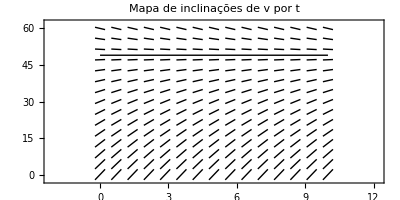

```mathematica
Show[campo,dvdtNulo]
```

Ratos do campo e corujas

ⅆp/ⅆt=0.5 p - 30 15

```mathematica
ω[x_,y_]:={1,.5y-450}
```

```mathematica
ratosTempo=VectorPlot[ω[x,y],{x,0,5},{y,800,1000},VectorStyle->{Arrowheads[0]},AspectRatio->1/10];
```

```mathematica
Solve[ω[x,y][[2]]/ω[x,y][[1]]==0,y]
```

{{y→900.}}

```mathematica
equil=Plot[900,{x,0,5},PlotStyle->{Thin,Black}];
```

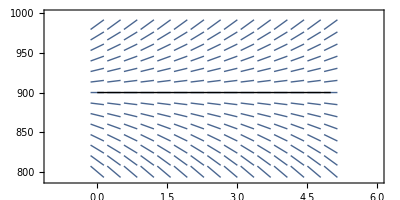

```mathematica
Show[ContourPlot[y==0,{x,-1,6},{y,790,1000},AspectRatio->1/2,ContourStyle->{Black}],ratosTempo,equil]
```